```mathematica
ωp = 6.18;      (* unit: eV *)
γ = 20 10^-3; (* unit: eV *)
ϵ[ω_] := 1 - ωp^2/(ω (ω + I γ));
```

```mathematica
α[ω_] := (ϵ[ω]-1)/(ϵ[ω]+2);        (* unit: 4 Subscript[πϵ, 0] a^3 *)
```

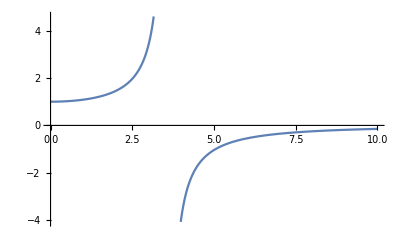

```mathematica
Plot[Re[α[ω]], {ω, 0, 10}]
```

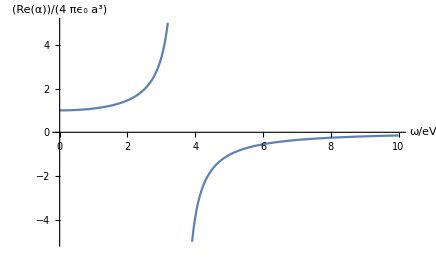

```mathematica
Show[Plot[Re[α[ω]], {ω, 0, 10}, PlotRange->{-5, 5}],AxesLabel->{HoldForm[ω/eV],HoldForm[Re[α]/(4 Subscript[πϵ, 0] a^3)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

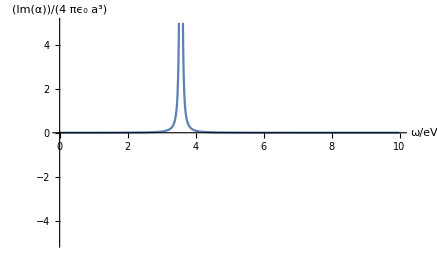

```mathematica
Show[Plot[Im[α[ω]], {ω, 0, 10}, PlotRange->{-5, 5}],AxesLabel->{HoldForm[ω/eV],HoldForm[Im[α]/(4 Subscript[πϵ, 0] a^3)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
o = 0.01; L = 20;
```

NIntegrate::ncvb: 在接近 {ν} = {3.59313} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.59638-0.00437491 ⅈ 和 0.139404.

NIntegrate::ncvb: 在接近 {ν} = {3.59313} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.6887-0.00505757 ⅈ 和 0.148148.

NIntegrate::ncvb: 在接近 {ν} = {-3.51625} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.43997+0.0034095 ⅈ 和 0.12439.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

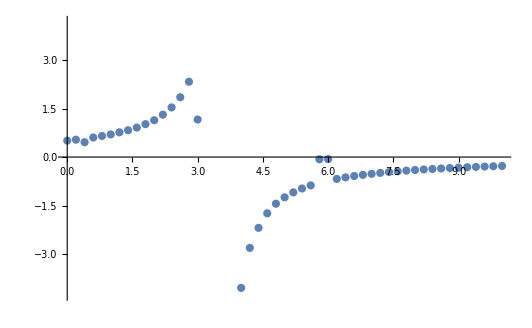

```mathematica
ListPlot[Table[{ω, -1/π Re[N[∫_-L^L Im[α[ν]]/(ω - ν + ⅈ o)ⅆν]]}, {ω, 0, 10, 0.2}]]
```

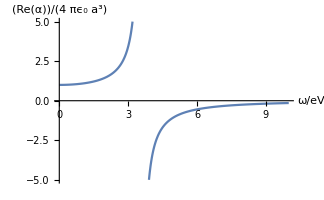
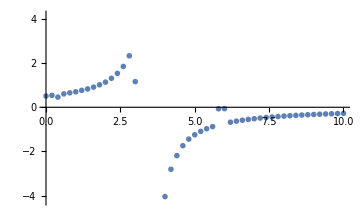
```mathematica
Show[-Graphics-,-Graphics-]
```

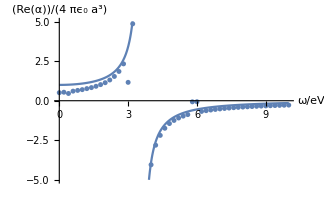

```mathematica
{ω, -1/π Re[N[∫_-50^50 Im[α[ν]]/(ω - ν + ⅈ 0.000000000000000001)ⅆν]]} /. ω -> 0
```

NIntegrate::inumr: 在以 {{-50,50}} 为界的区域内，对于所有采样点，计算被积函数 -(38.1924 Im[1/(ν (ⅈ/50+ν) (3-38.1924/(ν Plus[«2»])))])/((0.+1.×10^-18 ⅈ)-ν+ω) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {ν} = {-3.51718} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.51697+3.94888×10^-19 ⅈ 和 0.417279.

{0,0.482865}